# Gravitational Wave Calculations for PBHs

## Initial Definitions

Initial functions and constants that will be of use. Here, c is the speed of light in vacuum, G is Newton’s gravitational constant, MSol is the mass of the sun. All units are in SI units.

```mathematica
c=2.997*^8;
G=6.674*^-11;
MSol=1.988*^30;
```

PBHMass is the expected mass of the primordial black holes in solar masses. This value was chosen as the maximum mass of a PBH that would theoretically be able to fully ring up the ADMX cavity.
PBHAvgDistance is the expected average distance of a primordial black hole merger event from Earth, in parsecs. This is estimated based on the assumption that all dark matter in the universe is composed of primordial black holes of mass PBHMass, based on a density calculation.

```mathematica
PBHMass=10^-11;
PBHAvgDistance=10^-3;
```

Rs[M] takes a mass M in kg and returns its Schwarzschild radius in meters.
NewtonianGWFrequency[M,R] takes a mass M in kg and an orbital radius R in meters to return a frequency in Hertz. This equation is 7.194 in Carroll.
NewtonianGWStrain[M,R,r] takes a mass M in kg, an orbital radius R in meters, and a distance from observer r in meters to return a strain strength. This equation is 7.195 in Carroll.
pcTom[r] converts a radius r in parsecs to meters.
mTopc[r] converts a radius r in meters to parsecs.
SchwarzschildISCO[M] takes a mass M in kg and gives the innermost stable circular orbital radius in meters for a Schwarzschild black hole of that size.
KerrISCO[M] takes a mass in M in kg and gives the ISCO for a Kerr black hole of that size.
kgToSM[M] converts a mass M in kilograms to solar masses.
SMTokg[M] converts a mass M in solar masses to kilograms.

```mathematica
Rs[M_]=2G M/c^2;
NewtonianGWFrequency[M_,R_]=c Sqrt[Rs[M]]/(10Sqrt[R^3]);
NewtonianGWStrain[M_,R_,r_]=Rs[M]^2/(r R);
pcTom[r_]=3.086*^16 * r;
mTopc[r_]=3.086*^-16*r;
SchwarzchildISCO[M_]=3Rs[M];
KerrISCO[M_]=4.5Rs[M];
kgToSM[M_]= M/MSol;
SMTokg[M_]= M MSol;
```

## ADMX: Specifications

According to Berlin et al. in “Detecting High-Frequency Gravitational Waves with Microwave Cavities” (https://arxiv.org/pdf/2112.11465.pdf), ADMX has these specific parameters associated with it:

```mathematica
ADMXFreqLowerBound=0.65;
ADMXFreqUpperBound=1.02;
CouplingConstant=0.1;
ADMXMagneticField=7.5;
ADMXVolume=136;
ADMXTemperature=0.6;
ADMXQuality=8*^4;
ADMXTimeIntegration=2;
```

Here, the frequencies are given in GHz, the coupling constant is an estimated value for the coupling of  to , the magnetic field strength is given in Tesla, the volume is given in liters, the temperature is given in Kelvin, the quality factor is unitless, and the time of integration is given in minutes.

Equation 26 in the paper gives their estimated strain as a result of inspiraling masses at a distance R from Earth; they do not explain where they got this. We define it here.
h0[R,M,ω] takes a distance from Earth R in parsecs, a mass in solar masses, and a gravitational wave frequency ω, and returns the expected strain.

```mathematica
h0[R_,M_,ω_]=10^-29 * (1/R)(M/(10^-11))^(5/3)(ω)^(2/3);
```

We can compare their strain equation to the Newtonian approximation in Carroll:

```mathematica
NewtonianGWStrain[SMTokg[PBHMass],2SchwarzchildISCO[SMTokg[PBHMass]],PBHAvgDistance]
NewtonianGWFrequency[SMTokg[PBHMass],2SchwarzchildISCO[SMTokg[PBHMass]]]
SchwarzchildISCO[SMTokg[PBHMass]]
h0[PBHAvgDistance,PBHMass,ADMXFreqUpperBound]
```

4.92388×10^-6

6.90241×10^13

8.86299×10^-8

1.01329×10^-26

So, here are some interesting things. Interesting features here are that the strain differs by about 20 orders of magnitude. The Newtonian approximation estimates that it’ll be an (absurdly) strong GW coming at us, at a very high frequency (about  GHz). This would be pretty energetic for a gravitational wave. The innermost stable circular orbit of these PBHs is about  meters, which is tiny - on the order of 10 nanometers. But, this was done at ISCO, which is not really reasonable. We should be trying to detect them well before ISCO since ISCO is the upper bound. We’ll do this later.

The paper’s formula estimates it’ll be a very weak GW coming towards us, at about 1.02 GHz. This frequency works fine (although we inserted it by hand), but the strain is so low that ADMX can’t detect it! We’ll have to play around and see what happens with that.

Also interesting is the different dependencies. The Newtonian approximation is ultimately based on the masses of the objects, their orbital distance from one another, and their distance from the observer. The paper’s approximation requires only their distance from the observer, the masses of the objects, and the frequency of the waves that are emitted. I’m not sure where this comes from; I imagine they got their formula using some general relativity techniques. I’m still not sure if the Newtonian approximation is working here (I’m not sure if we should even reasonably expect it to work - we’re dealing with black holes, which are inherently relativistic, even if they are very small); beyond the obvious issues of what we’re seeing at ISCO, we can also do some other calculations to showcase its issues.

## The Newtonian Case

First, we can calculate the orbital radius that would actually give us frequencies we can observe at ADMX for a particular mass of  solar masses (this is what is estimated to be viable by the paper):

```mathematica
Solve[ADMXFreqLowerBound*10^9==NewtonianGWFrequency[SMTokg[PBHMass],r],r]
Solve[ADMXFreqUpperBound*10^9==NewtonianGWFrequency[SMTokg[PBHMass],r],r]
```

{{r→-0.000198749-0.000344244 ⅈ},{r→-0.000198749+0.000344244 ⅈ},{r→0.000397498}}

{{r→-0.00014718-0.000254922 ⅈ},{r→-0.00014718+0.000254922 ⅈ},{r→0.000294359}}

```mathematica
OuterSensitivityRadiusNewtonian=0.00039749831155469907
InnerSensitivityRadiusNewtonian=0.00029435906279067295
```

0.000397498

0.000294359

So here, we can see that the frequencies that ADMX can pick up are at about  meter separation (discarding imaginary solutions). This is eminently reasonable for black holes with a Schwarzschild radius of around  meters. Now let’s see how long these black holes will live for. The orbit of an inspiraling binary object decays as:



Let us solve this differential equation and see what our solutions look like, using the initial condition that we are starting at the furthest separation that ADMX can detect:

```mathematica
DSolve[{r'[t]==-64 G^3 SMTokg[PBHMass]^2(2SMTokg[PBHMass])/(5r[t]^3 c^5),r[0]==OuterSensitivityRadiusNewtonian},r[t],t]
```

{{r[t]→0.000396555 (1.00955-4. t)^(1/4)}}

So how long does it take for this system to fully inspiral? What about reaching the upper limit of the frequency that ADMX can detect?

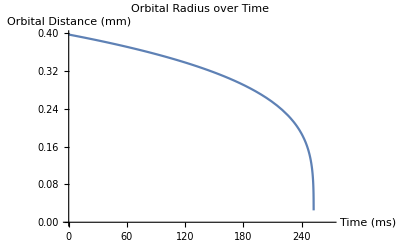

{{t→0.252386}}

{{t→0.176487}}

```mathematica
Plot[0.0003965550633154335*10^3 (1.0095452592355654-4. t/1000)^(1/4), {t,0,270},PlotLabel->"Orbital Radius over Time",AxesLabel->{"Time (ms)","Orbital Distance (mm)"}]
Solve[0==0.0003965550633154335 (1.0095452592355654-4. t)^(1/4), t]
Solve[InnerSensitivityRadiusNewtonian==0.0003965550633154335 (1.0095452592355654-4. t)^(1/4), t]
```

So it’ll take a quarter of a second for these black holes to finish merging (and only a sixth of a second will be spent radiating in the sensitive zone)! Note that in this time, we’re also expecting our black holes to be emitting gravitational waves of frequency twice that of the orbital frequency. We can figure out what the frequencies look like throughout this range:

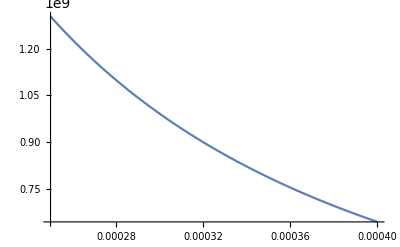

```mathematica
Plot[NewtonianGWFrequency[SMTokg[PBHMass],r],{r,0.00025,0.0004}]
```

This is twice the orbital frequency, so if we divide these by 2, we’ll get the instantaneous orbital frequencies of our objects in revolutions per second. If we also insert the solution to our differential equation for r as a function of time, we can get the frequency as a function of time, and integrate to get the total number of revolutions.

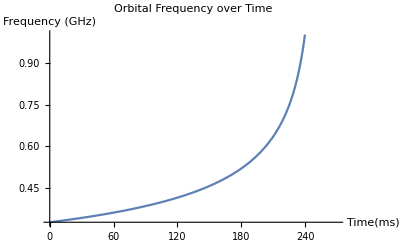

6.93074×10^10

```mathematica
OrbitalRadius[t_]=0.0003965550633154335 (1.0095484243225772-4. t)^(1/4);
Plot[NewtonianGWFrequency[SMTokg[PBHMass],OrbitalRadius[t/1000]]/2*(10^-9),{t,0,270},PlotLabel->"Orbital Frequency over Time", AxesLabel->{"Time(ms)","Frequency (GHz)"}]
Integrate[NewtonianGWFrequency[SMTokg[PBHMass],OrbitalRadius[t/1000]]/2,{t,0,176.48738418186297}]
```

Wow, that is a lot of revolutions! About what you’d expect to see, though, at these frequencies. The quality factor of ADMX is approximately , and we want to see the number of revolutions be higher than this in order to fully ring up our cavity. This is far more than we need to fully ring up the cavity, which suggests that we can actually radiate for a much shorter time period and ADMX should still be able to see this signal. Notice, though, that it’ll appear in ADMX as a very short-lived signal - ADMX should only pick it up for around 1/5 of a second. Here, we are also neglecting any effects from gravitational redshifts. And, of course, we’re assuming that Kepler’s laws and all those are actually valid in this regime. We’re also assuming that the angular momentum of the system is essentially conserved and that the energy loss from the gravitational waves is negligible. We also assume that there aren’t any other effects going on during the inspiral that are causing it to decay faster or slower (for example, if they’re charged black holes). What about the strength of the gravitational waves we’ll see?

```mathematica
NewtonianGWStrain[SMTokg[PBHMass],InnerSensitivityRadiusNewtonian,pcTom[PBHAvgDistance]]
NewtonianGWStrain[SMTokg[PBHMass],OuterSensitivityRadiusNewtonian,pcTom[PBHAvgDistance]]
```

9.60826×10^-26

7.1152×10^-26

These seem pretty reasonable! Probably far beyond our detection capabilities, but maybe not forever. They’re also actually quite close to the weaker end of . Let’s see what happens as we adjust the distances:

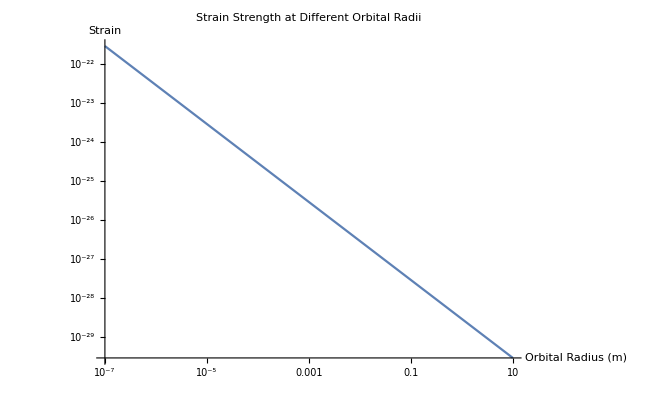

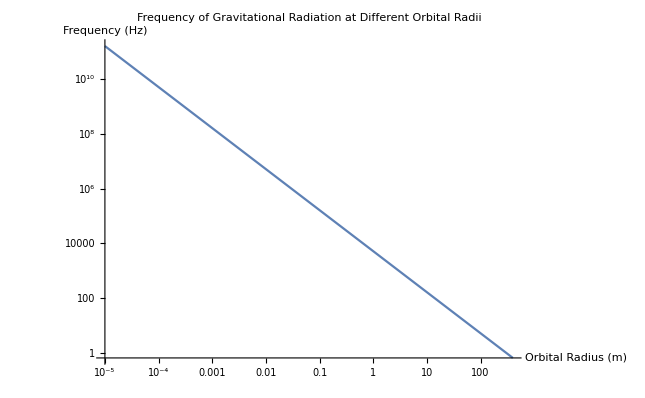

```mathematica
LogLogPlot[NewtonianGWStrain[SMTokg[PBHMass],R,pcTom[PBHAvgDistance]],{R,10^-7,10^1},PlotLabel->"Strain Strength at Different Orbital Radii",AxesLabel->{"Orbital Radius (m)","Strain"}]
LogLogPlot[NewtonianGWFrequency[SMTokg[PBHMass],r],{r,10^-5,4*10^2},PlotLabel->"Frequency of Gravitational Radiation at Different Orbital Radii", AxesLabel->{"Orbital Radius (m)","Frequency (Hz)"}]
```

The top plot shows our strain strength at different radii, while the bottom plot shows the frequency of the waves emitted at different radii. Notably, we hit LIGO frequencies between around 1 m and 100 m (LIGO bandwidth is 10 Hz to  Hz. And already at around  m (corresponding to a frequency of  Hz), we’re at a point already where LIGO has no hope of seeing those strains - going that far out, the GWs are orders of magnitude too small. It’s also worth noticing here that I’m neglecting redshifts of the gravitational waves (presumably occurs) and assuming that angular momentum and energy of the system is generally conserved (not true since the GWs carry it away), and that the system itself is only inspiraling because of GWs (i.e. not charged black holes, no other weird effects, no other gravitational effects nearby). For a final plot, we’ll just plot strain against frequency and cut out the middleman:

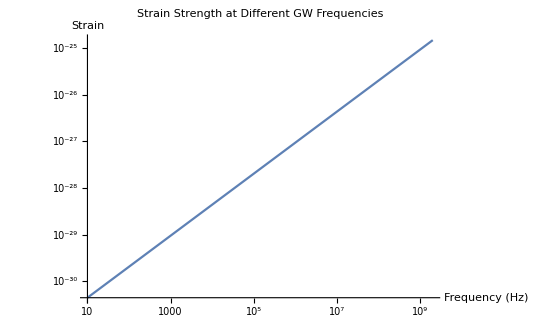

```mathematica
RadiusAtFrequency[M_,ω_]=(c Sqrt[Rs[M]]/(10ω))^(2/3);
LogLogPlot[NewtonianGWStrain[SMTokg[PBHMass],RadiusAtFrequency[SMTokg[PBHMass],ω],pcTom[PBHAvgDistance]],{ω,10,2*10^9},PlotLabel->"Strain Strength at Different GW Frequencies",AxesLabel->{"Frequency (Hz)","Strain"}]
```

Of course, this is assuming that we are looking at  solar mass black holes a distance  pc from Earth.

Let’s see how the strain looks at various distances from Earth:

```mathematica
Plot3D[NewtonianGWStrain[SMTokg[PBHMass],R,pcTom[r]],{R,10^-7,10},{r,10^-6,10^-2},ScalingFunctions->{"Log","Log","Log"},AxesLabel->{"Orbital Radius (m)","Distance from Observer (pc)","Strain"},PlotLabel->"Strain of GW Emitted During Inspiral"]
```

-Graphics3D-

So we can see that as we bring the objects in closer to Earth, we expect to see stronger strains. Actually, we can even just plot this as a function of frequency and distance:

```mathematica
Plot3D[NewtonianGWStrain[SMTokg[PBHMass],RadiusAtFrequency[SMTokg[PBHMass],ω],pcTom[r]],{ω,10,10^9},{r,10^-6,10^-2},ScalingFunctions->{"Log","Log","Log"},AxesLabel->{"GW Frequency (Hz)","Distance from Observer (pc)","Strain"},PlotLabel->"Strain of GW Emitted During Inspiral"]
```

-Graphics3D-

Notice that here, even at  pc from Earth, LIGO band isn’t sensitive enough to see the predicted signal, but the ADMX band is.

Overall, the Newtonian approximation predicts we can’t see anything, either at ADMX or at LIGO...but it also predicts that if we could see strains of order  in the near future, we definitely still wouldn’t have seen them at LIGO.

## Using the Paper’s Equations

Alright, so now let’s see what happens with the paper’s case. To begin with, we’ll repeat most of the calculations we did in the Newtonian case to see how things work here. We’ll start by looking at the inspiral time. This should be essentially the same equation, just with different constants, since the time evolution of the radius should be the same. We would like to start detecting these well before ISCO, but how far from ISCO is hard to say. Let’s see if we can calculate it. The time evolution of the frequency relative to the radius is given in the paper on page 12 as:



This is in Hertz. The units work fine, so there shouldn’t be any factors of hbar or c that need to be inserted. Note the authors also comment that as we get closer to ISCO, the signals will evolve in time according to  rather than using the above equation we used. So:

```mathematica
PaperFrequency[M_,r_]=14*10^-6/M*(2SchwarzchildISCO[SMTokg[M]]/r)^(3/2);
```

This takes a mass in solar masses and a radius in meters, and outputs a frequency in GHz.

```mathematica
Solve[PaperFrequency[PBHMass,r]==ADMXFreqLowerBound,r]
Solve[PaperFrequency[PBHMass,r]==ADMXFreqUpperBound,r]
```

{{r→0.00295633}}

{{r→0.00218925}}

```mathematica
PaperOuterRadius=0.0029563337534422424;
PaperInnerRadius=0.0021892511431207446;
```

Alright, these are roughly in agreement with the Newtonian approximation; they’re on the order of millimeters, instead of tenths of a millimeter. Here’s a plot!

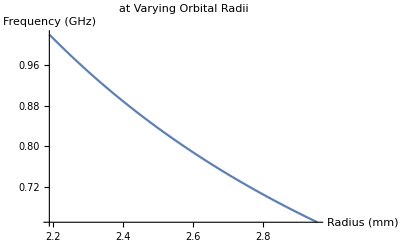

```mathematica
Plot[PaperFrequency[PBHMass,r/1000],{r,PaperInnerRadius*1000,PaperOuterRadius*1000},PlotLabel->" at Varying Orbital Radii",AxesLabel->{"Radius (mm)","Frequency (GHz)"}]
```

Again, it would be nice to know how long this takes. So we’ll fall back to our differential equation again and solve it; the solution will be of the same form, but we have a different starting point and different constants as a result.

```mathematica
DSolve[{r'[t]==-64 G^3 SMTokg[PBHMass]^2(2SMTokg[PBHMass])/(5r[t]^3 c^5),r[0]==PaperOuterRadius},r[t],t]
```

{{r[t]→0.000396555 (3088.87-4. t)^(1/4)}}

```mathematica
Solve[0==0.0003965550633154335 (3088.8715585835034-4. t)^(1/4),t]
Solve[PaperInnerRadius==0.0003965550633154335 (3088.8715585835034-4. t)^(1/4),t]
```

{{t→772.218}}

{{t→539.993}}

Wow, this actually takes a relatively long time! We’ll be radiating in the bandwidth that ADMX can see for about 9 minutes. This means we’ve fully rung up the cavity effortlessly (it should only take about  seconds). The only problem is that the strain will be super weak; the paper’s equation for the strain tells us that our strains will be:

```mathematica
h0[PBHAvgDistance,PBHMass,ADMXFreqLowerBound]
h0[PBHAvgDistance,PBHMass,ADMXFreqUpperBound]
```

7.5037×10^-27

1.01329×10^-26

On the order of  at the strongest. The paper estimates that ADMX will be sensitive to frequencies between  and , so we’ve got some problems. Note that even LIGO is only sensitive to around  strains at 100 Hz. Let’s check their value for ADMX’s sensitivity using the equation they use. This function takes in the desired frequency ωg in GHz, the coupling strength of  to  η, the experiment background magnetic field B in Tesla, the volume of the cavity V in liters, the quality factor Q, the temperature of the system T in Kelvin, the frequency bandwidth ν in kHz, and the time of integration t in minutes, to return a theoretical strain sensitivity.

```mathematica
ADMXSensitivity[ωg_,η_,B_,V_,Q_,T_,ν_,t_]=(ωg)^(3/2)(0.1/η)(8/B)(0.1/V)^(5/6)(10^5/Q)^(1/2)(T/1)^(1/2)(ν/10)^(1/4)(1/t)^(1/4)*3*10^-22;
```

So...why is there a 2π in there? Everywhere else in the paper, ωg has been in GHz, but now it seems to be an angular frequency in radians per second, not an ordinary frequency. I’m going to assume they just implicitly meant ωg / 2π everywhere else in the paper it appeared, since that would make the most sense. Well, let’s see what happens:

```mathematica
ADMXSensitivity[ADMXFreqLowerBound,0.1,7.5,136,8*10^4,0.6,(ADMXFreqUpperBound-ADMXFreqLowerBound)*10^6,2]
ADMXSensitivity[ADMXFreqUpperBound,0.1,7.5,136,8*10^4,0.6,(ADMXFreqUpperBound-ADMXFreqLowerBound)*10^6,2]
```

4.14535×10^-24

8.14876×10^-24

Wow, that is pretty sensitive and doesn’t seem likely! If we were to restore the 2π  the authors have in their equation, we’d scale the sensitivity up even more by about a factor of 10 since 2π is roughly 10. But there are a ton of parameters that affect this, and it’s likely that there are some parameters that are a bit optimistic here.  Either way, this still isn’t sensitive enough to pick up the strains we estimate we’d see by about two orders of magnitude. Also, this is quite sensitive compared to the estimates the authors of the paper had for the sensitivity; they estimated the maximum sensitivity would be around  at the highest resonant frequency of the signal mode.

Well, ADMX can’t see it. But let’s see if LIGO should be able to see this (it shouldn’t, since the strain should decrease as the system time-devolves and the frequencies decrease). Let’s go backwards, using our time evolution equation for our frequencies, and see what r we need to be emitting gravitational waves in the 10 Hz to 10,000 Hz regime (where LIGO is sensitive):

```mathematica
Solve[PaperFrequency[PBHMass,r]==10^-8,r]
Solve[PaperFrequency[PBHMass,r]==10^-5,r]
```

{{r→477.928}}

{{r→4.77928}}

Alright, so somewhere between 4.8 and 488 m, the PBHs will be emitting GWs in LIGO’s bandwidth. This kind of agrees with the Newtonian approximation. What kinds of GW strains will we see as they sweep through this regime?

```mathematica
h0[PBHAvgDistance,PBHMass,10^-8]//N
h0[PBHAvgDistance,PBHMass,10^-5]//N
```

4.64159×10^-32

4.64159×10^-30

Very weak ones, that LIGO wouldn’t see, according to their equation. Let’s look at a plot:

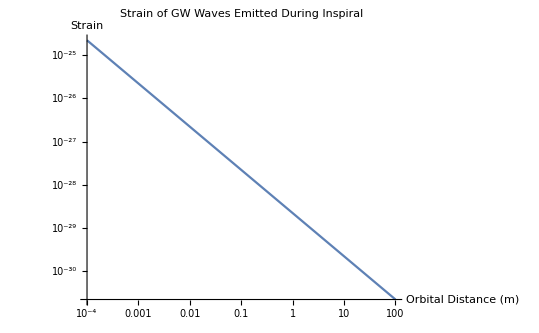

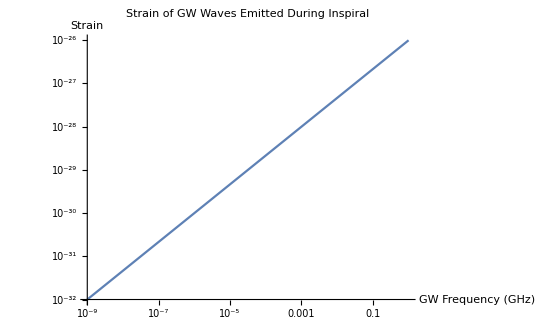

```mathematica
LogLogPlot[h0[PBHAvgDistance,PBHMass,PaperFrequency[PBHMass,r]],{r,10^-4,10^2},AxesLabel->{"Orbital Distance (m)","Strain"},PlotLabel->"Strain of GW Waves Emitted During Inspiral"]
LogLogPlot[h0[PBHAvgDistance,PBHMass,ω],{ω,10^-9,1},AxesLabel->{"GW Frequency (GHz)","Strain"},PlotLabel->"Strain of GW Waves Emitted During Inspiral"]
```

```mathematica
Plot3D[h0[d,PBHMass,ω],{d,10^-6,10^-3},{ω,10^-9,10^1},ScalingFunctions->{"Log","Log","Log"},AxesLabel->{"Distance from Observer (pc)","GW Frequency (GHz)","Strain Strength"},PlotLabel->"Strain of GW Waves Emitted During Inspiral"]
```

-Graphics3D-

Notably here, even if we bring the PBH distance from Earth in pretty close, the strains are still too weak for LIGO to see while they are radiating in its bandwidth. However, if we’re only a milliparsec from Earth, once we get to ADMX bandwidths, we’ll actually definitely see them. The odds of this happening are, uh, not great. We could, of course, also do what we did for the Newtonian approximation:

What if we use the Newtonian approximation? That far out, surely the Newtonian approximation is valid:

```mathematica
NewtonianGWStrain[SMTokg[PBHMass],4.77928,pcTom[PBHAvgDistance]]
NewtonianGWStrain[SMTokg[PBHMass],477.928,pcTom[PBHAvgDistance]]
```

5.91779×10^-30

5.91779×10^-32

Very weak ones that LIGO shouldn’t see. Bummer. But hey, the paper and the Newtonian approximation are in agreement, which is very cool. We also have that the strains are in agreement, to within one order of magnitude, which is also pretty decent. But, in both cases, we predict LIGO can’t see them at all.

## Varying Mass and Distance

The above calculations all assume generally the same thing, that we’re looking at masses of  solar masses and distances around  pc from Earth. But we can vary these parameters and see what happens - perhaps we’ll find at some mass or radius, we might be able to see the strains with modern tech. The constraints on mass and distance come from density - we presume that the PBHs form some part of dark matter. At , PBHs can actually form all of dark matter in agreement with modern observations, and the average distance is then calculated using the density of dark matter. As we increase the masses, the distance has to increase as well then, since the density goes . But at different masses, I think there might be issues with observation - we probably should have seen PBH effects already if they were much bigger, or much smaller. Let’s ignore this and pretend that the PBHs are always 100% of dark matter. Then, they will have to satisfy:

```mathematica
DistanceFromMass[M_]=(M/(PBHMass/PBHAvgDistance^3))^(1/3);
```

Let’s see what our strains look like when we use this. We should remember that at 1 solar mass, the Schwarzschild radius is about 2 kilometers, so the orbital radii for masses of that size should really be in the ballpark of  “Significantly more than  m”, with  being the cutoff for our frequencies.

```mathematica
Plot3D[NewtonianGWStrain[SMTokg[M],R,pcTom[DistanceFromMass[M]]],{M,10^-11,10^1},{R,10^1,10^6},ScalingFunctions->{"Log","Log","Log"},AxesLabel->{"Mass ()","Orbital Radius (m)","Strain"},PlotLabel->"Strain of GW Emitted During Inspiral By Different Masses"]
Rs[10^-11]
```

-Graphics3D-

These are rather powerful GWs, even allowing for the cutoff at around 1,000 m for a solar mass PBH (which isn’t real). Looking at the bandwidths:

```mathematica
Plot3D[{NewtonianGWStrain[SMTokg[M],RadiusAtFrequency[SMTokg[M],ω],pcTom[DistanceFromMass[M]]],10^-24(1-HeavisideTheta[ω-10^4])},{M,10^-11,10^1},{ω,10^1,10^9},ScalingFunctions->{"Log","Log","Log"},AxesLabel->{"Mass ()","GW Frequency (Hz)","Strain"},PlotLabel->"Strain of GW Emitted During Inspiral By Different Masses",PlotLegends->SwatchLegend[{"Strain of GW Waves","LIGO Sensitivity"}]]
```

-Graphics3D-

Alright, so this is kind of a confusing plot, but basically anything above the blue plane LIGO should have seen already in that band. This essentially means that we can’t expect to see merger events between PBHs greater in size than  around  to , since we’d have already seen them at LIGO (assuming that the mass density of PBHs is a constant). Anything lower than that seems to be fair game, though, so now let’s look at those in the GHz frequency regime:

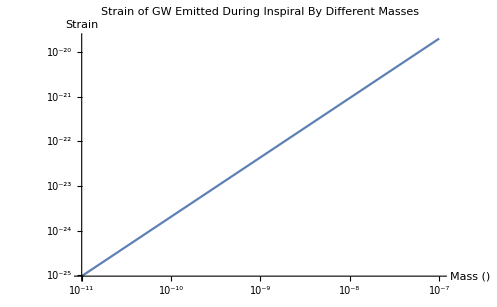

```mathematica
LogLogPlot[NewtonianGWStrain[SMTokg[M],RadiusAtFrequency[SMTokg[M],10^9],pcTom[DistanceFromMass[M]]],{M,10^-11,10^-7},AxesLabel->{"Mass ()","Strain"},PlotLabel->"Strain of GW Emitted During Inspiral By Different Masses"]
```

So anything greater than  or so might be visible to ADMX! Now let’s repeat this analysis, but using the paper’s equations rather than the Newtonian approximations:

```mathematica
Plot3D[{h0[DistanceFromMass[M],M,ω],10^-24(1-HeavisideTheta[ω-(10^-5)])},{M,10^-11,10^1},{ω,10^-9,1},ScalingFunctions->{"Log","Log","Log"},AxesLabel->{"Mass ()","Frequency (GHz)","Strain"},PlotLabel->"Strain of GW Emitted During Inspiral By Different Masses",PlotLabel->"Strain of GW Emitted During Inspiral By Different Masses",PlotLegends->SwatchLegend[{"Strain of GW Waves","LIGO Sensitivity"}]]
```

-Graphics3D-

Here, it looks like this equation precludes mergers of masses greater than  to  or so. (I don’t know why the LIGO Sensitivity plane has a delta function). So, let’s see what that range looks like:

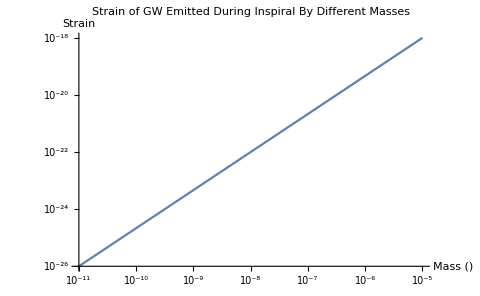

```mathematica
LogLogPlot[h0[DistanceFromMass[M],M,1],{M,10^-11,10^-5},AxesLabel->{"Mass ()","Strain"},PlotLabel->"Strain of GW Emitted During Inspiral By Different Masses"]
```

Here, we expect to be able to see masses of greater than around  or  with ADMX.